## Bayesian Statistics, Exam 1

## Tuesday, Sept. 24, 2024 — Covering Young Sections 1-9

## 1. Propagation of Error (3 pts)

The force of air resistance is can be written F=c v^2, where v is the speed, and c is some constant.

(a) Write out the four terms on the right-hand side of F+ΔF=c·(v+Δv)^2, so that you have a new equation for F+ΔF.



(b) Put  F=c v^2 into what the left-hand-side of the equation that you got in (a). Then do a little cancellation to get a formula for ΔF. If Δv is small, then (Δv)^2 and higher powers of  Δv are very small. Discard the (Δv)^2 terms to get an approximate formula for  ΔF.







(c) Often times, it is nicer to compute the “fractional change in F,” which is by definition (Δ F)/F, than it is to compute ΔF itself. Starting with what you got in (c) and again using F=c v^2, simplify the fractional change in F as much as you can:

(Δ F)/F=

## 2. Mean and Standard Deviation (2 pts)

I promised to give you all the formulas. Here is the definition of the mean.

And here is Young’s definition of the standard deviation and the variance.

Here is an unusual set of 7 measurements:

3, 2, 4, 7, 6, 5, 1

It is unusual (and would not likely happen) because each measured value from 1 to 7 occurs exactly once.

(a) What is the mean of these 7 measurements? HINT: Just arrange them in order, and it will become pretty obvious. And what is the variance, σ^2, for these 7 measurements. JUST WRITE DOWN EVERY TERM OF THE SUM YOU WOULD COMPUTE to get the variance, nice and tidily. No need to punch into the calculator until the next part.


(b) Ok, now grab a calculator, punch in and get an number for σ^2, the “variance.” Also take the square root and get a number for σ, “the standard deviation.” HINT: I made the unusual data set so that these would come out really easy. You don’t even need a calculator.

## 3. Histograms and Normalized Histograms (3 pts)

(a) Use the grid below to make a histogram of the data in Problem 2.

NOTE: Please center each histogram bar that you draw over the corresponding data value. As an example, your 3 bar should be centered on 3, not sit to the right of 3.

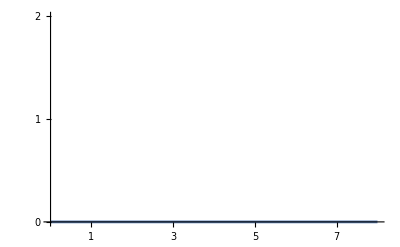

```mathematica
Plot[0, {x, 0, 8},PlotRange->{{0,8},{0,2}},Ticks->{Range[1,7,1],Range[0,2,1]}]
```

(b) The total area of the histogram bars above is 7, right? Divide every bar by 7 to get a normalized histogram and put the normalized histogram on the grid below. 1/7 is about 0.14.

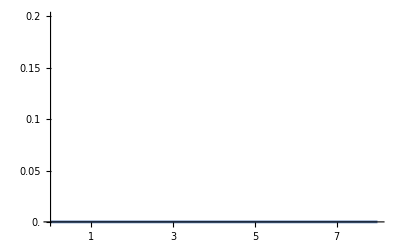

```mathematica
Plot[0, {x, 0, 8},PlotRange->{{0,8},{0,0.2}},Ticks->{Range[1,7,1],Range[0,0.2,0.025]}]
```

(c) What percentage of the histogram lies in bins 3, 4, and 5?

## 4. Poisson Distributions (3 pts)

In Problem 2(a) , you found the mean of a distribution. In the Poisson distribution, if the mean is 4 then a=4 in this formula

P_a(n)=e^-a a^n/(n!)

(a) Now you are really going to need a calculator. Fill in the three values in this table that I blanked out.

```mathematica
a=4;
blankout = " ";
pa[n_]:=If[n==5||n==6||n==7, blankout, NumberForm[N[Exp[-a]a^n/Factorial[n]], {2,2}]];
TableForm[Table[{n, pa[n]}, {n, {1, 2, 3, 4,5, 6, 7}}]]
```

1 | 0.07
2 | 0.15
3 | 0.20
4 | 0.20
5 |  
6 |  
7 |

(b) Graph the Poisson distribution on the grid below. Use little x’s to mark the values.

```mathematica
Plot[0, {x, 0, 8},PlotRange->{{0,8},{0,0.2}},Ticks->{Range[1,7,1],Range[0,0.2,0.025]}]
```

-Graphics-

(c) What percentage of this Poisson distribution lies in bins 3, 4, and 5?

## 5. Gaussian Distributions (3 pts)

In Problem 4(a) , you made a table for a Poisson distribution. 4 isn’t a very big number. Poisson and Gaussian distributions only start to look like each other when the mean and standard deviation are large numbers. Well, let’s see how good the agreement is for a mean of 4 and a standard deviation of 2.

P_(m,σ)(x)=1/(√(2π)σ)e^(-(x-m)^2/(2 σ^2))

(a) Fill in the three values in this table that I blanked out:

```mathematica
m=4;σ=2;pmsigma[x_]:=If[x==5||x==6||x==7, blankout, NumberForm[N[1/(Sqrt[2Pi]σ)Exp[-(x-m)^2/(2 σ^2)]], {2,2}]];
TableForm[Table[{N[x,{2, 2}], pmsigma[x]}, {x, {1, 2, 3, 4,5, 6, 7}}]]
```

1. | 0.06
2. | 0.12
3. | 0.18
4. | 0.20
5. |  
6. |  
7. |

(b) Graph the Gaussian distribution on the same graph as you used for Problem 4(b) Use little o’s to mark the values, so we can see the difference from the little x’s you made for the Poisson distribution.

(c) What percentage of this Gaussian distribution lies in bins 3, 4, and 5?

## 6. The Logic of Probability (1 pt)

In the picture above is a plane with three engines on each wing. If all three engines fail on one wing, the plane cannot get home. In other words, you need at least one engine working on each wing to get home.

If three engines fail at random, what are the odds that the plane can get home?

Name ______________________________________

1.              / 3
2.              / 2
3.              / 3
4.              / 3
5.              / 3
6.              / 1

TOTAL          / 15